```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];

dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];
SetDirectory[folder];

FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,dataDump,POL2018-03-18.dat,pumpQWP,reallyNiceData,temp,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-03-22_Ei=37eV","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
Length[polFileNames]
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]];
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
```

963

```mathematica
runFiles={
<|"exfn"->"173218","polFile"-> "173525","fscan"->"171723","aouts"-> {432},"rbAbs"->"171118","temp"->Range[103,121,3],"runs"->7,"pumpTemp"->{27.97},"studyVariable"->"temp","stringId"->"3-21-18_Ei=37_BGP=100_TempStudy"|>,
<|"exfn"->"135815","polFile"-> "142140","fscan"->"140421","aouts"-> {288},"rbAbs"->"135815","runs"->7,"pumpTemp"->{27.97},"temp"->{121},"stringId"->"3-22-18_Ei=37_BGP=100_realign"|>,
<|"exfn"->"175540","polFile"-> "175803","fscan"->"174045","aouts"-> {264},"temp"->{121},"rbAbs"->"173440","runs"->15,"pumpTemp"->{27.97},"stringId"->"3-22-18_Ei=20_BGP=350"|>,
<|"exfn"->"003602","polFile"-> "003909","fscan"->"002109","aouts"-> {312},"rbAbs"->"001504","runs"->4,"pumpTemp"->Range[28.205,27.855,-.035],"temp"->{121},"studyVariable"->"pumpTemp","stringId"->"3-23-18_Ei=55_BGP=350_pumpDetStep"|>,
<|"exfn"->"211657","polFile"-> "211922","fscan"->"210203","aouts"-> {240},"rbAbs"->"205558","runs"->7,"temp"->Range[121,136,3],"studyVariable"->"temp","stringId"->"3-23-18_Ei=37_BGP=350_TempStudy"|>,
<|"exfn"->"150839","polFile"-> "151019","fscan"->"145345","aouts"-> {288},"rbAbs"->"144740","runs"->4,"studyVariable"->"pumpTemp","pumpTemp"->Join[Range[28.065,28.184,.017],Range[28.200,28.305,.035]],"stringId"->"3-24-18_Ei=37_BGP=350_pumpDetStep"|>,
<|"stringId"->"3-25-18_polarizationStepSizeStudy","polFile"-> "095728","aout"->{288},"temp"->{136},"runs"->7,"studyVariable"->"stepSize","pumpTemp"->{27.97},"stepSize"->{60,30,20,15}|>,
<|"stringId"->"3-25-18_Ei=37_BGP=350_StepTemp","rbAbs"->"202833","fscan"->"203439","exfn"->"204934","polFile"-> "205156","aouts"-> {264},"runs"->7,"studyVariable"->"temp","pumpTemp"->{27.970},"temp"->Range[136,148,3]|>,
<|"stringId"->"3-26-18_Ei=50_BGP=700","rbAbs"->"102202","fscan"->"102939","exfn"->"104434","polFile"-> "104656","aouts"-> {96},"runs"->7,"pumpTemp"->{27.970},"temp"->{148}|>,
<|"stringId"->"3-26-18_Ei=35_BGP=770","rbAbs"->"181656","fscan"->"182432","exfn"->"183926","polFile"-> "184231","aouts"-> {144},"runs"->10,"pumpTemp"->{27.970},"temp"->{130}|>,
<|"stringId"->"3-27-18_Ei=35_BGP=700_tempStep","rbAbs"->"000126","fscan"->"000902","exfn"->"002400","polFile"-> "002623","aouts"-> {144},"runs"->7,"pumpTemp"->{27.970},"studyVariable"->"temp","temp"->Range[130,125,-1]|>,
<|"stringId"->"3-27-18_Ei=35_Tres=125_BGPStep","rbAbs"->"161446","fscan"->"162224","exfn"->"163721","polFile"-> "163945","aouts"-> {120},"runs"->4,"pumpTemp"->{27.970},"temp"->{125},"BGP"->{770,550,260,120},"studyVariable"->"BGP"|>,
<|"stringId"->"3-28-18_Ei=2_tempStep","rbAbs"->"021322","fscan"->"022234","exfn"->"023737","polFile"-> "023917","aouts"-> {264},"runs"->15,"pumpTemp"->{27.970},"temp"->Range[125,121,-2],"studyVariable"->"temp"|>,
<|"exfn"->"135648","polFile"-> "135828","fscan"->"142410","aouts"-> {312},"pumpPower"->{72.3,58.6,37.5,13.8,3.9,1.2},"pumpTemp"->{27.97},"studyVariable"-> "pumpPower","stringId"->"Ei=100_BGP=100_Eh=33_PowerStudy"|>,
<|"exfn"->"003216","polFile"-> "003823","fscan"->"010356","aouts"-> {24},"pumpPower"->{115,94,63,26,5.3,-.3},"pumpTemp"->{27.97},"studyVariable"-> "pumpPower","stringId"->"Ei=100_BGP=100_Eh=33_PowerStudy2"|>
};
run=runFiles[[12]];
stringId=run["stringId"]
runs=run["runs"]; (*The number of Electron Polarization Runs*)
aouts=run["aouts"]; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"none","s+","s-"};
energies=aouts;
model=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,run["exfn"]];
For[l=1;l≤Length[energies],l++,
energies[[l]]=model[aouts[[l]]];
];

temperatures=run["temp"]


firstFscan=GetIndexOfFilenameFromTimestamp[scanFiles,run["fscan"]]
(* Rb Polarization file processing stuff *)
time={"pre","post"};
fscanCategories=<|run["studyVariable"]->run[run["studyVariable"]],"time"->time|>;
fileTimestamps=Dataset[OrganizeFscanFilesByCategories[scanFiles,firstFscan,fscanCategories,3]];


aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,run["exfn"]];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];


firstSignalFileIndex=GetIndexOfFilenameFromTimestamp[polFileNames,run["polFile"]];

fileNames=<||>;
allFiles=<||>;

categories=<|run["studyVariable"]->run[run["studyVariable"]],"pumpLight"->pumpLights|>;
signalFiles=Dataset[OrganizeFilesByCategories[polFileNames,firstSignalFileIndex,categories,runs]];

allStokes=<||>;

exFnIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,run["exfn"]];


For[m=1,m≤Length[categories[[1]]],m++,

fscanFileName=Normal[fileTimestamps[Select[#[Keys[categories][[1]]]==categories[[1]][[m]]&&#time=="pre"&]][All,"fileNames"]];

rbPolData=ProcessRbPolarizationFileSequence[scanFiles,fscanFileName[[1]],.225,3];

exFnData=ExcitationFunctionProcessor[excitationFileNames[[exFnIndex]]];
exFnIndex=exFnIndex+2;


For[i=1,i≤Length[categories[[2]]],i++,
signalFileNames=Flatten[Normal[signalFiles[Select[#cat1==categories[[1]][[m]]&]][Select[#cat2==categories[[2]][[i]]&]][All,"fileNames"]]];
stokes=CalculateAverageStokesFromFiles[signalFileNames,20.4*π/180,66.0*π/180,1.65];

AppendTo[stokes,Keys[categories][[2]]->categories[[2]][[i]]];
AppendTo[stokes,Keys[categories][[1]]->categories[[1]][[m]]];
AppendTo[stokes,"stringId"->run["stringId"]];

AppendTo[stokes,"n_rb"->rbPolData["n_rb"]];
AppendTo[stokes,rbPolData];
AppendTo[stokes,"p_rb"->rbPolData["p_rb"<>categories[[2]][[i]]]];
AppendTo[stokes,exFnData];

AppendTo[allStokes,signalFileNames[[1]]->stokes];
];

];
d=Dataset[allStokes];
Export["../analysis/"<>run["stringId"]<>".wdx",d];
```

3-27-18_Ei=35_Tres=125_BGPStep

{125}

298

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
d
```

Dataset[<>]

## Plot Stokes Parameters with Pump Lights in Different Colors for each energy

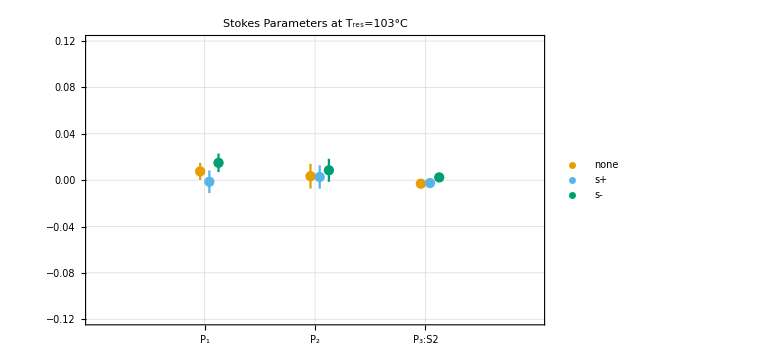
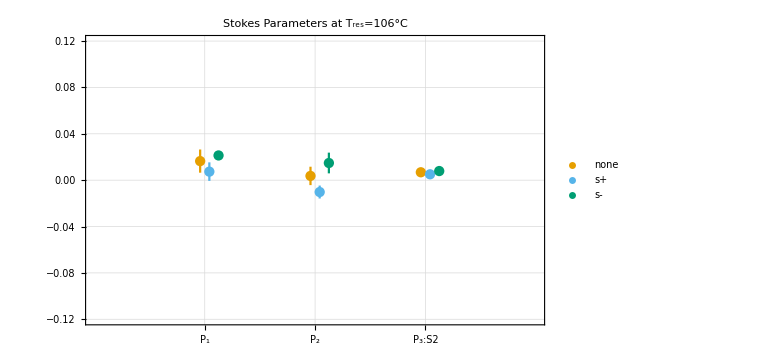
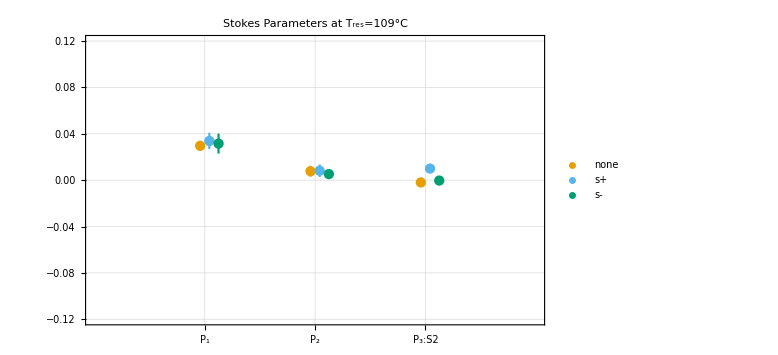
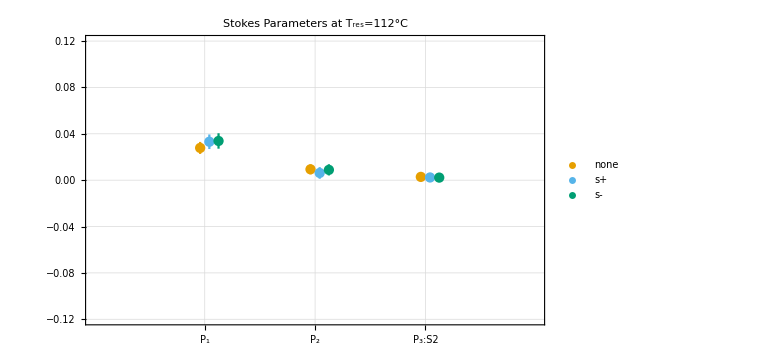
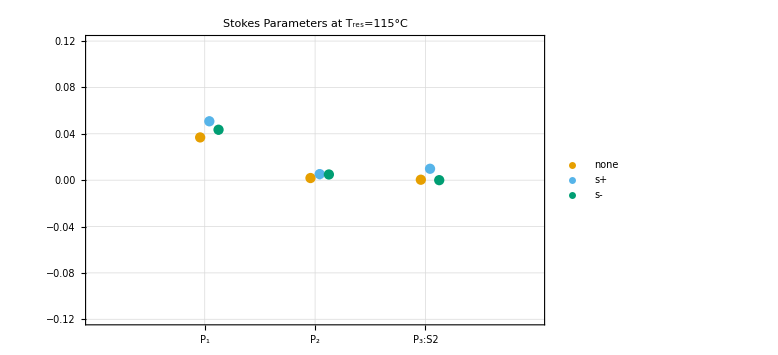
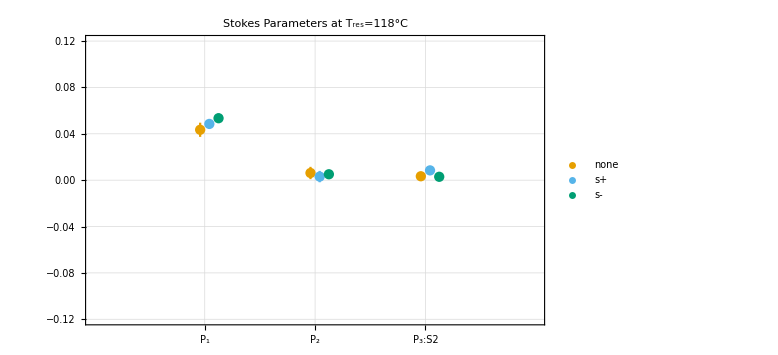
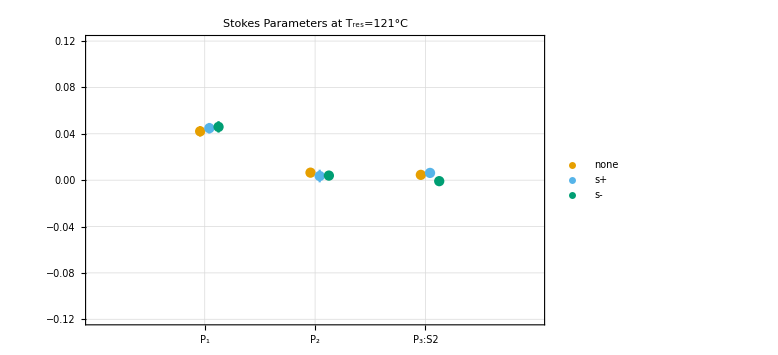
<|103→-Graphics-,106→-Graphics-,109→-Graphics-,112→-Graphics-,115→-Graphics-,118→-Graphics-,121→-Graphics-|>

```mathematica
energyPlots=<||>;
energyPlotsShort=<||>;

chosenStokes={"p1","p2","p3_s2"};
energy=1;
pumpLight=3;
For[m=1,m≤Length[categories["temp"]],m++,(*Study Variable*)
plots={};
plotsShort={};
dChooseCat1=d[Select[#[Keys[categories][[1]]]==categories[[1]][[m]]&]];
For[i=1,i≤Length[categories["pumpLight"]],i++,(* Pump Lights *)
plotData={};
plotDataShort={};
dChooseCat2=dChooseCat1[Select[#[Keys[categories][[2]]]== categories[[2]][[i]]&]];
s=GetStokesFromDatasetLine[dChooseCat2];
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1-.5((Length[categories[[2]]]-i)/Length[categories[[2]]]),s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
For[k=1,k≤Length[chosenStokes],k++,
AppendTo[plotDataShort,{{k-.25((Length[categories[[2]]]/2-i)/Length[categories[[2]]]),s[[1]][chosenStokes[[k]]]},ErrorBar[s[[2]][chosenStokes[[k]]<>"err"]]}];
];
height=.12;

AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{{0,6},{-height,height}},PlotStyle->colorBlindPallete[[i]],Frame->False,Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2"}},Automatic}]];
bottomTicks={{1,"P_1"},{2,"P_2"},{3,"P_3:S2"}};
AppendTo[plotsShort,ErrorListPlot[Legended[plotDataShort,pumpLights[[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{{0,4},{-height,height}},PlotStyle->colorBlindPallete[[i]],Frame->True,FrameTicks->{{Automatic,None},{bottomTicks,None}}]];

];
AppendTo[energyPlots,
categories[[1]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at T_res="<>ToString[categories[[1]][[m]]]<>"°C"]
];
AppendTo[energyPlotsShort,
categories[[1]][[m]]->Show[plotsShort,ImageSize->Large,PlotLabel->"Stokes Parameters at T_res="<>ToString[categories[[1]][[m]]]<>"°C"]
];
];
For[i=1,i≤Length[energyPlots],i++,
Export["../analysis/pumpLights_Energy="<>ToString[Keys[energyPlotsShort][[i]]]<>"_"<>stringId<>".png",energyPlotsShort[[i]],ImageResolution->200];
];
(*energyPlots*)
energyPlotsShort
```

## Plot Individual Stokes Parameters as a Function of Reservoir Temperature

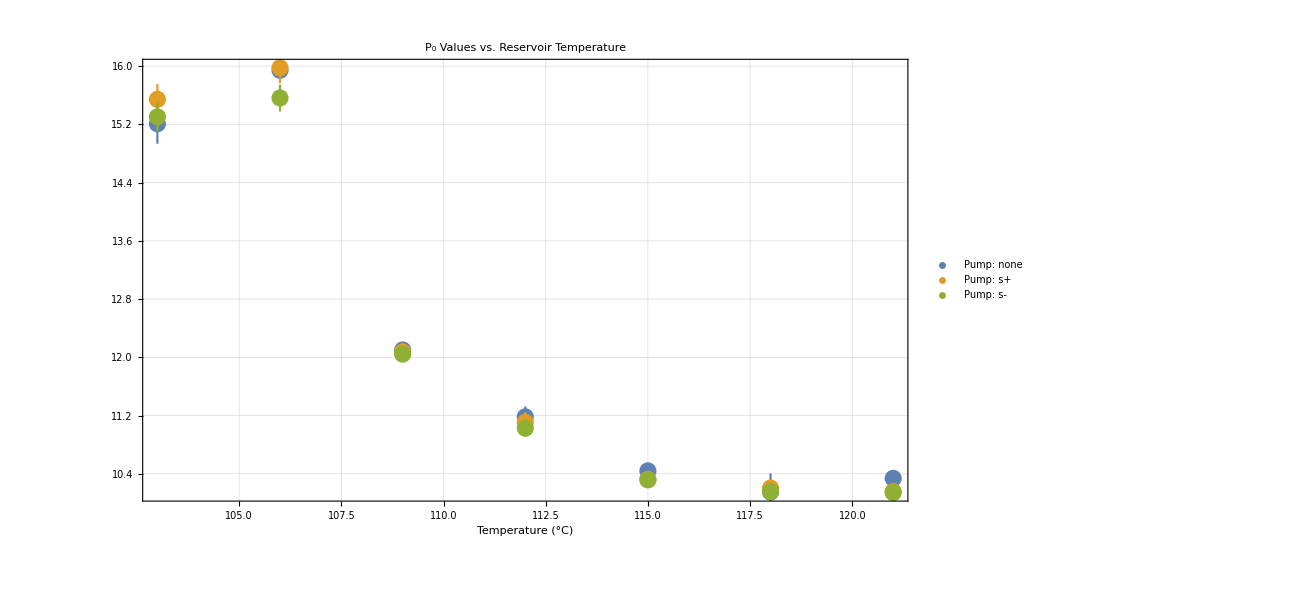
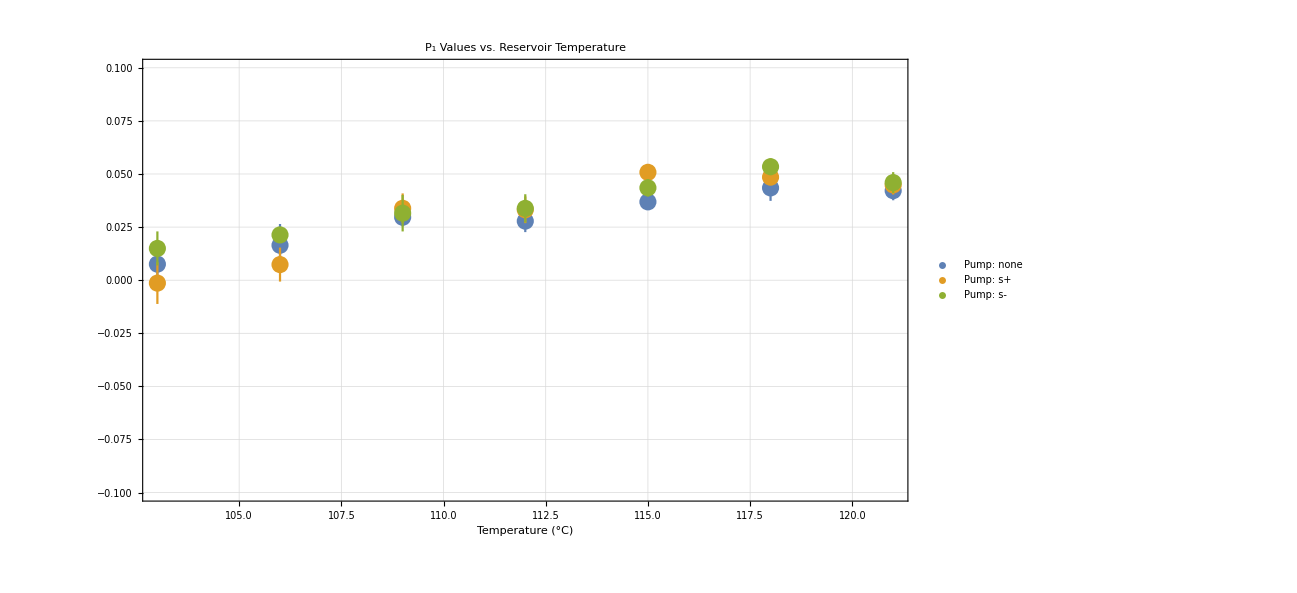
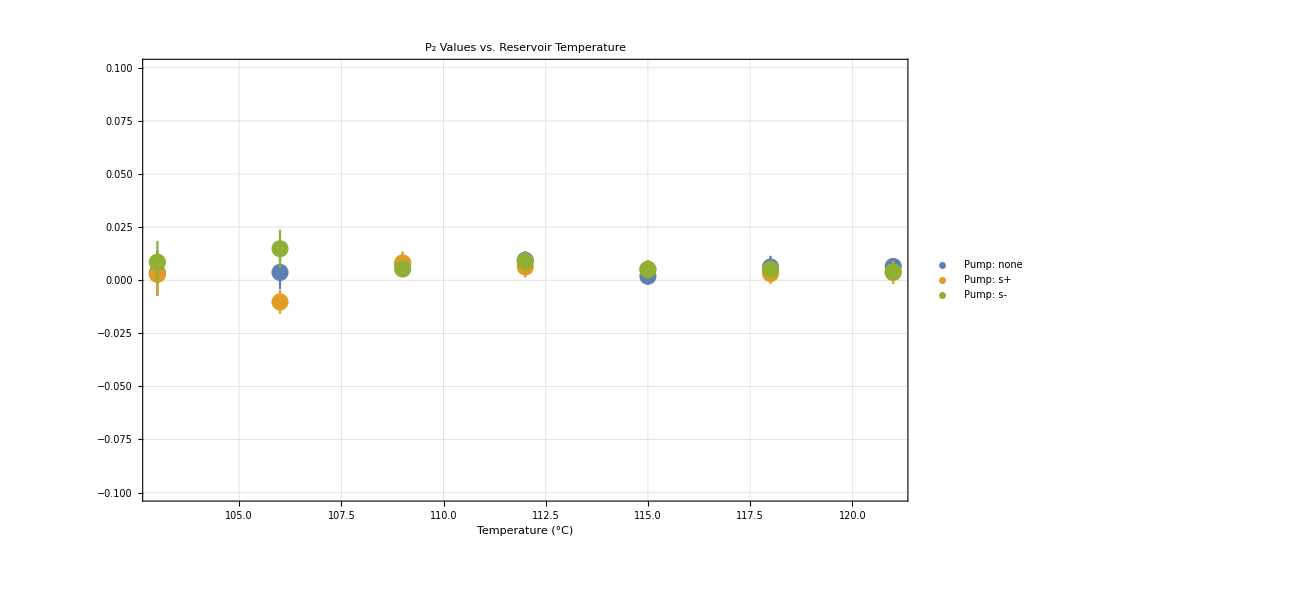
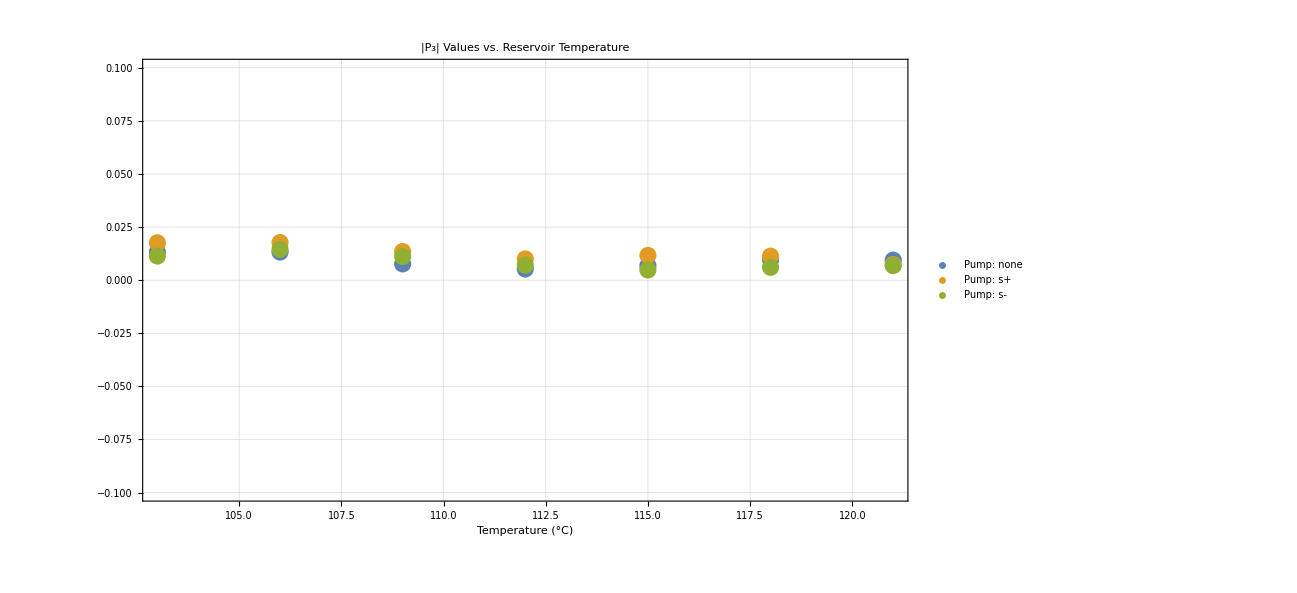
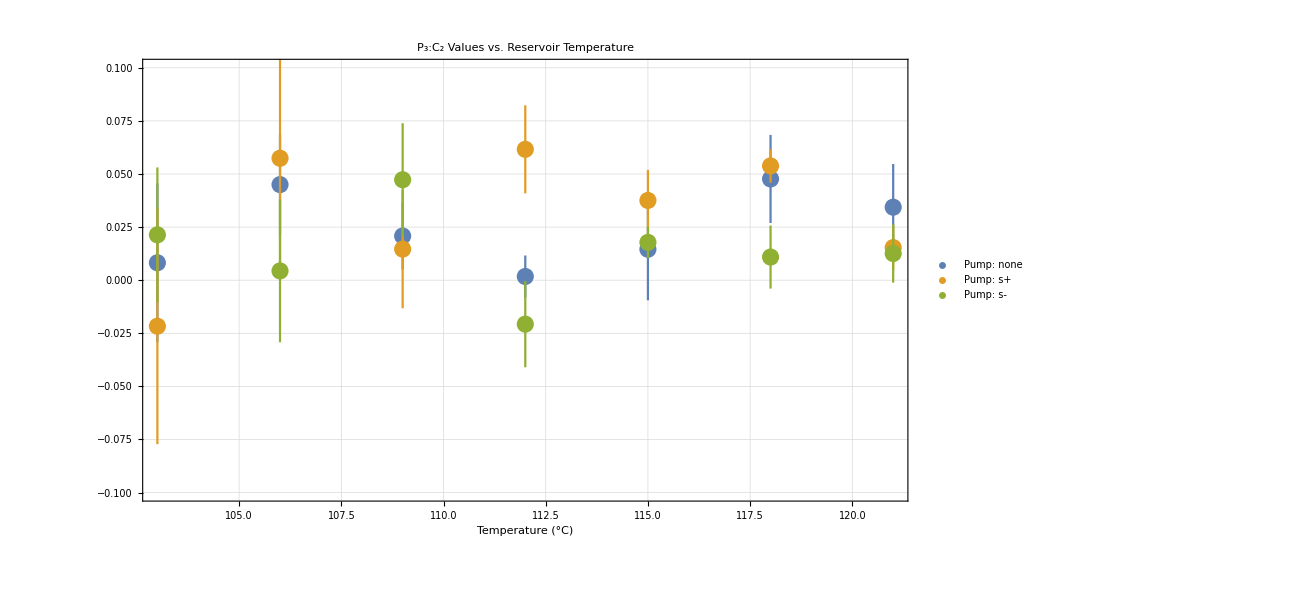
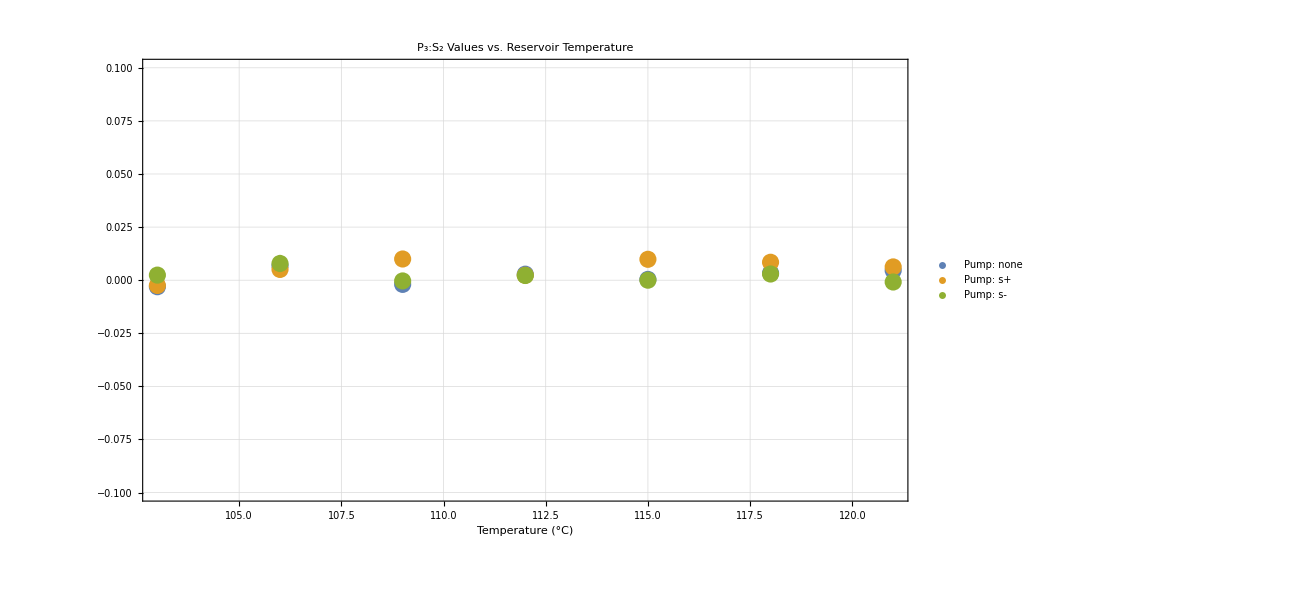
<|P_0→-Graphics-,P_1→-Graphics-,P_2→-Graphics-,|P_3|→-Graphics-,P_3:C_2→-Graphics-,P_3:S_2→-Graphics-|>

<|P_0→{{{103,15.3029},ErrorBar[0.198236]},{{106,15.5623},ErrorBar[0.185442]},{{109,12.0443},ErrorBar[0.052318]},{{112,11.0264},ErrorBar[0.117687]},{{115,10.3168},ErrorBar[0.0191374]},{{118,10.1542},ErrorBar[0.0135448]},{{121,10.1419},ErrorBar[0.0349921]}},P_1→{{{103,0.0149543},ErrorBar[0.00801303]},{{106,0.0213181},ErrorBar[0.00356307]},{{109,0.0315339},ErrorBar[0.00857601]},{{112,0.0338124},ErrorBar[0.00665235]},{{115,0.0434979},ErrorBar[0.0041148]},{{118,0.0534375},ErrorBar[0.0039722]},{{121,0.0459518},ErrorBar[0.00492595]}},P_2→{{{103,0.00851795},ErrorBar[0.00995467]},{{106,0.0148042},ErrorBar[0.00893402]},{{109,0.00524912},ErrorBar[0.00374547]},{{112,0.00887692},ErrorBar[0.00481121]},{{115,0.00490959},ErrorBar[0.00221159]},{{118,0.00509236},ErrorBar[0.00359622]},{{121,0.00394384},ErrorBar[0.00338941]}},|P_3|→{{{103,0.0113627},ErrorBar[0.00193548]},{{106,0.0145285},ErrorBar[0.00223581]},{{109,0.0111438},ErrorBar[0.00226814]},{{112,0.00708473},ErrorBar[0.00181499]},{{115,0.00480454},ErrorBar[0.00091671]},{{118,0.00607941},ErrorBar[0.00119546]},{{121,0.00688301},ErrorBar[0.00116659]}},P_3:C_2→{{{103,0.0213559},ErrorBar[0.031736]},{{106,0.0043673},ErrorBar[0.033582]},{{109,0.0472956},ErrorBar[0.0265877]},{{112,-0.0206919},ErrorBar[0.0203182]},{{115,0.0178196},ErrorBar[0.00733029]},{{118,0.0108946},ErrorBar[0.0148495]},{{121,0.0125649},ErrorBar[0.0137229]}},P_3:S_2→{{{103,0.00239319},ErrorBar[0.00324431]},{{106,0.0078654},ErrorBar[0.00404934]},{{109,-0.000352449},ErrorBar[0.00336531]},{{112,0.00220795},ErrorBar[0.0020771]},{{115,3.68573×10^-6},ErrorBar[0.00188071]},{{118,0.00291042},ErrorBar[0.00177872]},{{121,-0.000855168},ErrorBar[0.00265271]}}|>

```mathematica
plotLabels={"P_0","P_1","P_2","|P_3|","P_3:C_2","P_3:S_2"};
energy=1;
pumpLight=2;
valueOrError=1;

plotData=<||>;
plots=<||>;



For[k=1,k≤ Length[stokesNames],k++, (*stokes index*)
plotArguments={};
For[j=1,j≤ Length[pumpLights],j++,

dChooseCat1=d[Select[#pumpLight==pumpLights[[j]]&]];
plotPoints={};
onePumpOneStokes=dChooseCat1[All,{"temp",stokesNames[[k]],stokesErrNames[[k]]}][Values,All];
For[i=1,i≤Length[categories[[1]]],i++,(*Study Variable*)
plotDat=onePumpOneStokes[[i]];
plotPoint={{plotDat[[1]],plotDat[[2]]},ErrorBar[plotDat[[3]]]};
AppendTo[plotPoints,plotPoint];
];
AppendTo[plotData,plotLabels[[k]]->plotPoints];
If[k==1,plotRange={Automatic,Automatic},plotRange={-.1,.1}];
AppendTo[plotArguments,Legended[plotPoints,"Pump: "<>pumpLights[[j]]]];
];
AppendTo[plots,plotLabels[[k]]->
ErrorListPlot[plotArguments,PlotRange->plotRange,GridLines->Automatic,Frame->True,PlotLabel->  plotLabels[[k]]<> " Values vs. Reservoir Temperature",FrameLabel->{"Temperature (°C)",None}]];
];
Print[plots];
Print[plotData];

(*
For[i=1,i≤Length[plots],i++,
Export["../analysis/"<>pumpLights[[j]]<>"_stokesParameter="<>stokesNames[[i]]<>"_"<>stringId<>".png",plots[[i]],ImageResolution->200];
];
*)
(*Export["../analysis/stokesPlots.png",plots,ImageResolution->200]*)
```

```mathematica
Keys[allStokes]
```

{32.4584,25.0167,15.3426}

## Export TSV file with all Stokes Values

```mathematica
string="";
string=StringJoin[string,"energy\t"];
string=StringJoin[string,"Pumplight\t"];
For[a=1,a<=Length[stokesNames],a++,
string=StringJoin[string,ToString[Keys[allStokes[[1]][[1]][[1]]][[a]]]<>"\t"<>ToString[Keys[allStokes[[1]][[1]][[2]]][[a]]]<>"\t"];
];
string=StringJoin[string,"\n"];
For[b=1,b≤Length[energies],b++,

For[c=1,c≤Length[pumpLights],c++,
string=StringJoin[string,ToString[Keys[allStokes][[b]]]<>"\t"];
string=StringJoin[string,Keys[allStokes[[b]]][[c]]<>"\t"];
For[a=1,a<=Length[stokesNames],a++,
string=StringJoin[string,ToString[allStokes[[b]][[c]][[1]][[a]]]<>"\t"<>ToString[allStokes[[b]][[1]][[2]][[a]]]<>"\t"];
];
string=StringJoin[string,"\n"];
];
];
Export["tabulatedValues"<>stringId<>".txt",string];
```

## Plot Stokes Parameters vs. Energy with Pump Lights in Different Colors

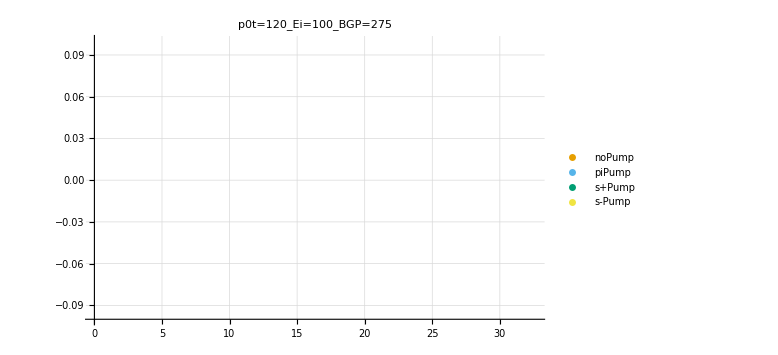
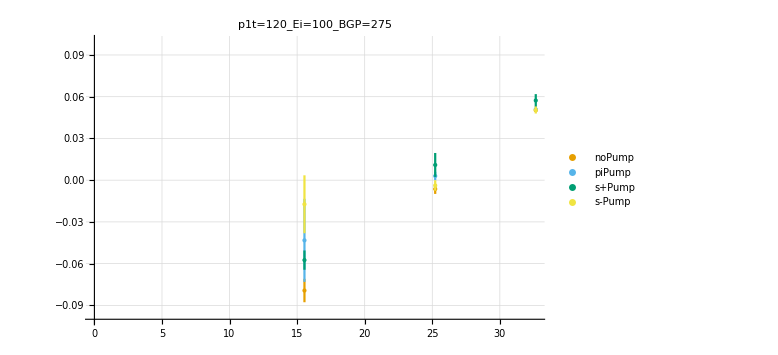
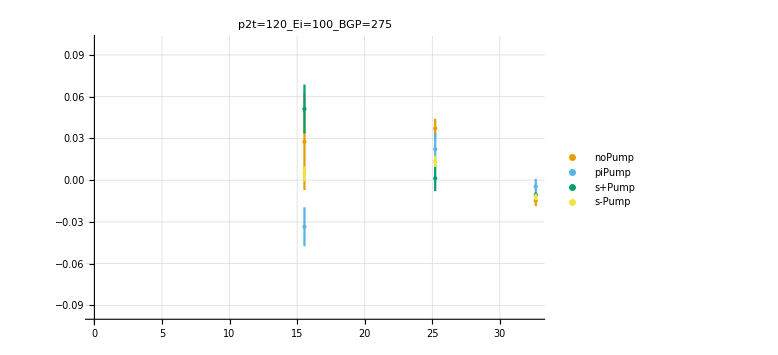
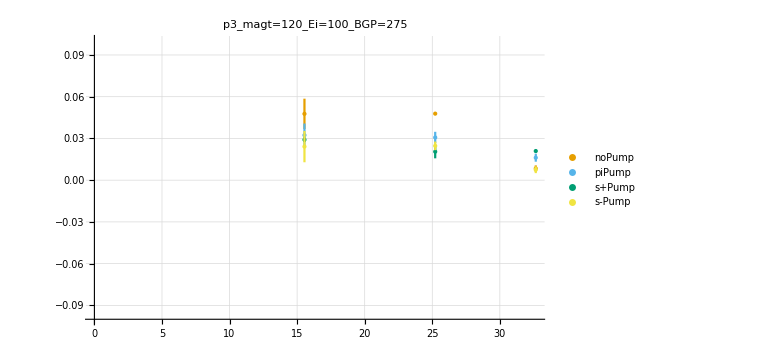
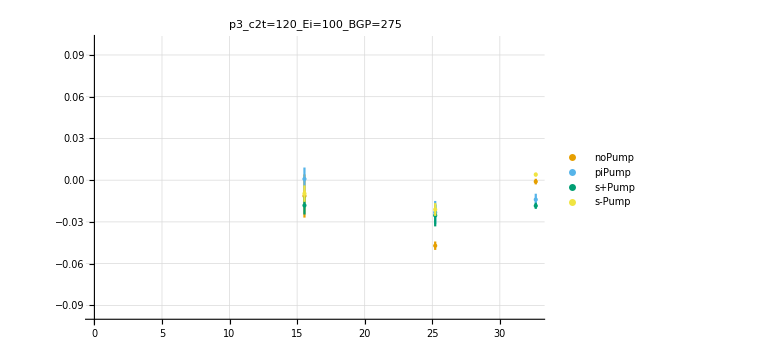
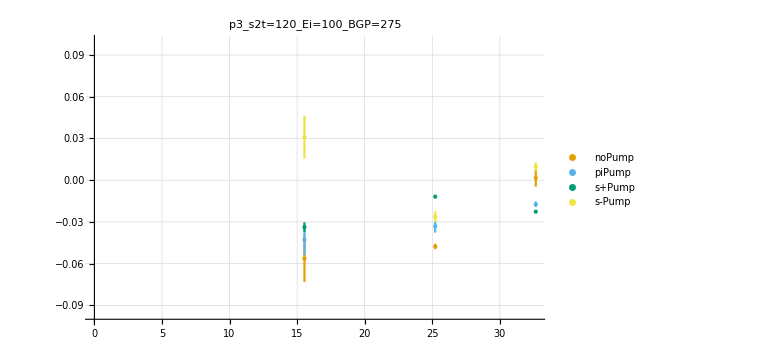
<|p0→-Graphics-,p1→-Graphics-,p2→-Graphics-,p3_mag→-Graphics-,p3_c2→-Graphics-,p3_s2→-Graphics-|>

```mathematica
stokesPlots=<||>;

energy=3;
pumpLight=4;
For[m=1,m≤Length[stokesNames],m++,
plots={};
For[i=1,i≤Length[pumpLights],i++,
plotData={};
For[k=1,k≤Length[energies],k++,
s=allStokes[[k]][[i]];
AppendTo[plotData,{{energies[[k]],s[[1]][[m]]},ErrorBar[s[[2]][[m]]]}];
];
height=.1;
AppendTo[plots,ErrorListPlot[Legended[plotData,pumpLights[[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{Automatic,{-.1,.1}},PlotStyle->colorBlindPallete[[i]],Frame->False]];
];
AppendTo[stokesPlots,
stokesNames[[m]]->Show[plots,ImageSize->Large,PlotLabel->stokesNames[[m]]<>stringId]
];
];
For[i=1,i≤Length[stokesPlots],i++,
Export[stokesNames[[i]]<>"_"<>stringId<>".png",stokesPlots[[i]],ImageResolution->200];
];
stokesPlots
```

## Display all raw data and averages

Pump Light: noPump, Energy: 32.4584

-Graphics-

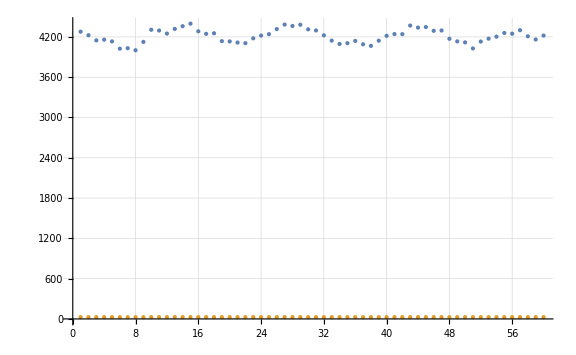

Pump Light: piPump, Energy: 32.4584

-Graphics-

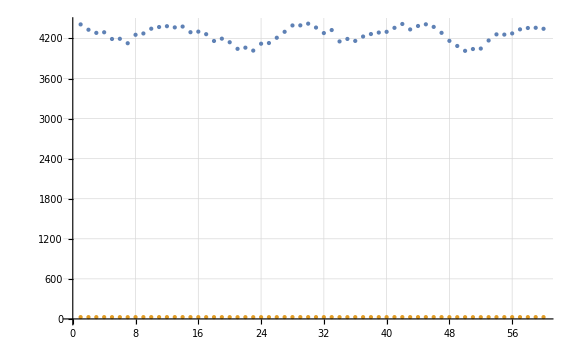

Pump Light: s+Pump, Energy: 32.4584

-Graphics-

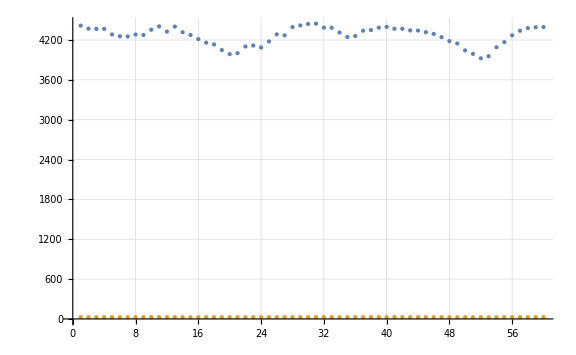

Pump Light: s-Pump, Energy: 32.4584

-Graphics-

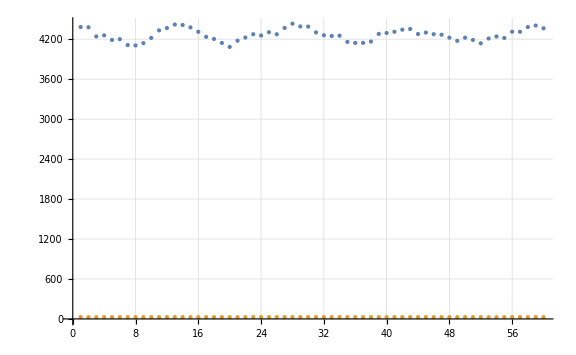

Pump Light: noPump, Energy: 25.0167

-Graphics-

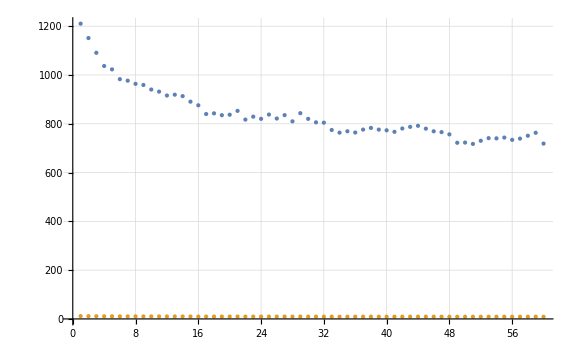

Pump Light: piPump, Energy: 25.0167

-Graphics-

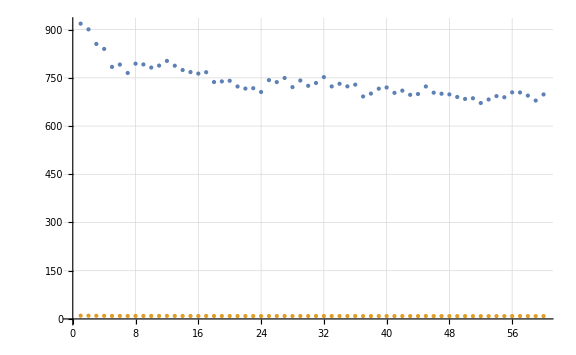

Pump Light: s+Pump, Energy: 25.0167

-Graphics-

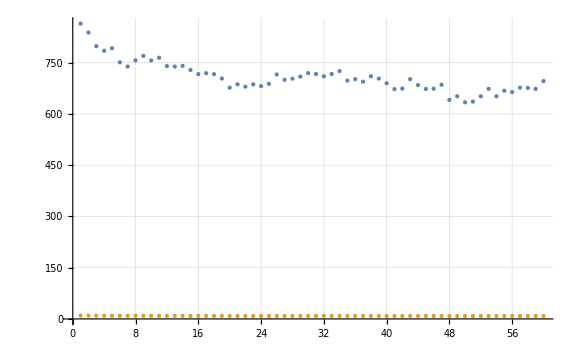

Pump Light: s-Pump, Energy: 25.0167

-Graphics-

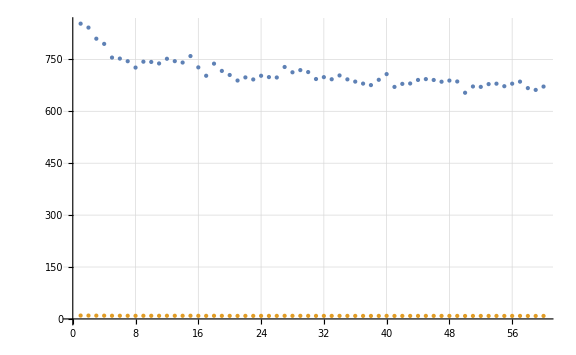

Pump Light: noPump, Energy: 15.3426

-Graphics-

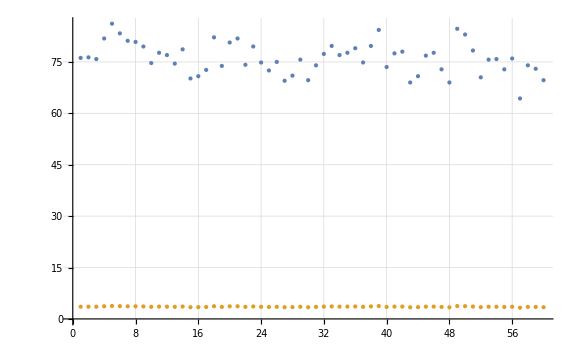

Pump Light: piPump, Energy: 15.3426

-Graphics-

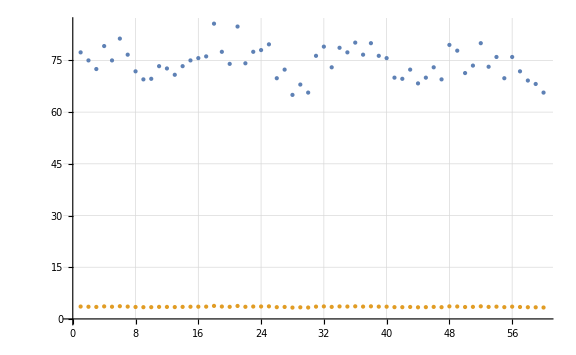

Pump Light: s+Pump, Energy: 15.3426

-Graphics-

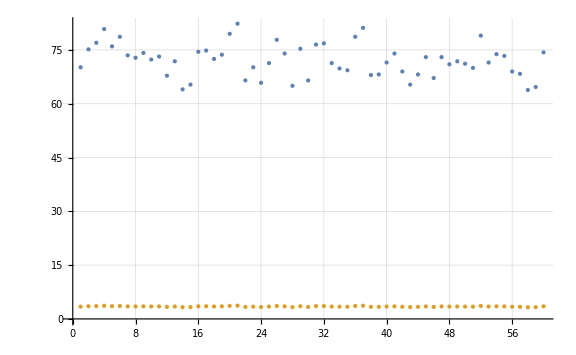

Pump Light: s-Pump, Energy: 15.3426

-Graphics-

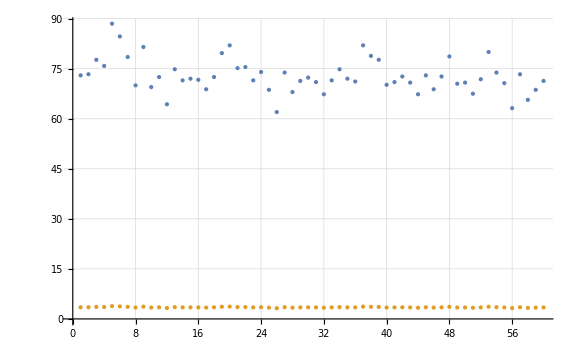

```mathematica
allStokes=<||>;
stokes=<||>;
allFiles=signalFiles;
For[j=1,j<=Length[energies],j++,
For[i=1,i<=Length[pumpLights],i++,
Print["Pump Light: "<>ToString[pumpLights[[i]]]<>", Energy: "<>ToString[energies[[j]]]]; 
fileNames=Flatten[Normal[signalFiles[Select[#cat2==pumpLights[[i]]&]][Select[#cat1==energies[[j]]&],"fileNames"]]];
Print[Rasterize[PlotListOfPolFileNames[fileNames]]];
Print[ListPlot[GetAverageCountRateFromFileNames[fileNames]]];
];
];
```

## Show representative Background Subtraction

```mathematica
darkFiles
```

Dataset[<>]

```mathematica
{{pumpStyle=1;
energy=1;
runNumber=2;
xAxisLabel="Retarder Position (60=1 Rev)";
imageRes=100;



averageDarkCounts=GetAverageCountRateFromFileNames[darkFiles[[pumpStyle]][[energy]]];
(*
molyFileNames=Flatten[Normal[molyFiles[Select[#cat2==pumpLights[[pumpStyle]]&]][Select[#cat1==energies[[energy]]&],"fileNames"]]];
molyFile=ImportFile[molyFileNames[[runNumber]]];
dwell=molyFile[[1]]["DWELL(s)"];
currentScale=molyFile[[1]]["SCALE"];

countRateData=Normal[molyFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[molyFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];


molyMinusDark=countRateData-averageDarkCounts[[1]];
molyMinusDarkPlot=ListPlot[{Legended[averageDarkCounts[[1]],"Dark Counts\n(4 run average)"],Legended[countRateData,"Representative\nMoly Count Rate"],Legended[molyMinusDark,"Moly Minus Dark"]},PlotLabel->"Moly Count Dark Subtraction",FrameLabel->{xAxisLabel,"Count Rate"}];

molyCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Moly Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

molyMinusDarkCurrentNorm=molyMinusDark/currentData;
molyMinusDarkCurrentNormPlot=ListPlot[molyMinusDarkCurrentNorm,PlotLabel->"Moly Minus Dark, Current Normalized",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}] ;

signalFileNames=Flatten[Normal[signalFiles[Select[#cat2==pumpLights[[pumpStyle]]&]][Select[#cat1==energies[[energy]]&],"fileNames"]]];
signalFile=ImportFile[signalFileNames[[runNumber]]];
dwell=signalFile[[1]]["DWELL(s)"];
currentScale=signalFile[[1]]["SCALE"];
mTorrHe=signalFile[[1]]["CVGauge(He)(Torr)"]/mTorr;

countRateData=Normal[signalFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[signalFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];
20.5

signalMinusDark=countRateData-averageDarkCounts[[1]];
signalMinusDarkPlot=ListPlot[{Legended[countRateData,"Raw Signal\nCounts"],Legended[signalMinusDark,"Raw Signal\nMinus Dark"]},PlotLabel->"Signal Minus Dark Counts",FrameLabel->{xAxisLabel,"Count Rate (Hz)"}];

signalCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Signal Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

signalMinusMoly=signalMinusDark/currentData-molyMinusDarkCurrentNorm ;
signalCurrentNormSubtractionPlot=ListPlot[{Legended[signalMinusDark/currentData,"Signal Minus Dark,\nCurrent Normalized"],Legended[molyMinusDarkCurrentNorm,"Moly Counts,\nCurrent Normalized"],Legended[signalMinusMoly,"Signal Minus Moly,\nCurrent Normalized"]},PlotLabel->"Signal Background Subtraction",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}];

grid=GraphicsGrid[{{molyMinusDarkPlot,signalMinusDarkPlot},
{molyCurrentPlot,signalCurrentPlot},
{molyMinusDarkCurrentNormPlot,signalCurrentNormSubtractionPlot}},ImageSize->{1510,Automatic}]

signalMinusMolyHeNormalized=signalMinusMoly/mTorrHe;
finalPlot=ListPlot[Legended[signalMinusMolyHeNormalized,"Signal Counts, background subtracted,\n helium pressure normalized."]]
fc=DFT[signalMinusMolyHeNormalized]
sine=1;
cosine=2;
signal=1;
error=2;
sin=fc[[sine]][[signal]];
cos=fc[[cosine]][[signal]];
sinBar=BarChart[Take[sin,{2,11}],PlotLabel->"Sin Fourier Coefficients",ChartLabels->{"S_1","S_2","S_3","S_4","etc."},Frame->True];
cosBar=BarChart[Take[cos,{2,11}],PlotLabel->"Cos Fourier Coefficients",ChartLabels->{"C_1","C_2","C_3","C_4","etc."},Frame->True];
fcPlot=GraphicsGrid[{{sinBar},{cosBar}}]
recreation[θ_]:=cos[[1]]+cos[[3]]Cos[2(θ*π/30)]+sin[[3]]Sin[2(θ*π/30)]+cos[[5]]Cos[4(θ*π/30)]+sin[[5]]Sin[4(θ*π/30)];
simulation=Plot[recreation[θ],{θ,0,60},PlotRange->{Automatic,{0,Automatic}}]
samplePol=Show[{finalPlot,simulation},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"Example Polarization Data",FrameLabel-> {"Polarimeter Position (60= 1 rev)","BS, Normalized Count Rate (Hz/nA/mTorr_He)"}]
SetDirectory[ParentDirectory[]<>"/analysis"]
Export["samplePolarization.png",samplePol,ImageResolution->200]
Export["sampleFC.png",fcPlot,ImageResolution->200]
Export["backGroundSubtractionSample.png",grid,ImageResolution->100]
SetDirectory[ParentDirectory[]<>"/data"]


PlotRawPolFromFileName[molyFiles["noPump"][[1]]]
molyExample=GetCurrentNormalizedMolyCountRateFromFileNames[molyFiles["noPump"][[1]],darkCounts];
ListPlot[molyExample[[1]],PlotLabel->"Example set of Moly Counts"]
*), □}}
```

Import::chtype: First argument 32.6584 is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Import::chtype: First argument 32.6584 is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-1},All].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of <||> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Null^6,□}}

## Electron Polarization Functions

```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large,LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},ImageSize->Large,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[ListLogPlot,BaseStyle->{FontSize->24},ImageSize->Large,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
stokesNames={"p0","p1","p2","p3_mag","p3_c2","p3_s2"};
stokesErrNames={"p0err","p1err","p2err","p3_magerr","p3_c2err","p3_s2err"};
nA=1*^-9;
mTorr=1*^-3;
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

(*Physical constants *)
c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(*cm*)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* cm^2*g/s *)
ν0=377107.463;  (* GHz *)
gHzToHz=1*^9;
nDensC=2*h/(c*re*fge*k*μ)*10^18; (* cm^2*g*s^-1  *  G^-1*cm^-1  *  cm^-1*s  *  cm^-1  *  g^-1*cm^-2*s^2*G  *)
(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)


alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_:1]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]]);
stokes];

(* 
Someday when I'm bored, I can try to implement the asoociation version of the stokes vectors. Today is not that day
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes=<||>;
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
AppendTo[stokes,stokesNames[[1]]->c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0])];
AppendTo[stokes,stokesNames[[2]]->2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[3]]->2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[4]]->Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]])];
AppendTo[stokes,stokesNames[[5]]->c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]])];
AppendTo[stokes,stokesNames[[6]]->-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]])];
stokes
];
*)

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["REV"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];



GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["DATAPPR"];
rev=files[[1]][[1]]["REV"];
scale=files[[1]][[1]]["SCALE"];
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

GetCurrentNormalizedMolyCountRateFromFileNames[fileNames_,darkCountsRate_]:=Module[{files},
files=ImportFile[fileNames];
GetCurrentNormalizedMolyCountRateFromFiles[files,darkCountsRate]
];

GetCurrentNormalizedMolyCountRateFromFiles[files_,darkCountsRate_]:=Module[{currentnA,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,currentScale},
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
currentScale=files[[i]][[1]]["SCALE"];
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
currentnA=current*10^(-currentScale)/nA;
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/dwell-darkCountsRate[[1]][[j]])/(nCycles*Abs[currentnA[[j]]]);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*currentnA[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*currentnA[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
rev=files[[i]][[1]]["REV"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,mTorrHe},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["DWELL(s)"];
nCycles=file[[1]]["REV"];
mTorrHe=file[[1]]["CVGauge(He)(Torr)"]/mTorr;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=((counts[[j]]/dwell-darkCountsRate[[1]][[j]])/Abs[current[[j]]]-molyCountsRate[[1]][[j]])/(nCycles*mTorrHe);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2*mTorrHe^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2*mTorrHe^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2*mTorrHe^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileBackgroundSubtractedStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileStokes[polFileName_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=GetCurrentNormalizedAverageCountRateFromFiles[{file}];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileCurrent[polFileName_]:=Module[{signal,stokes,file,rev,currentScale,currentValues,currentPlot,currentAvg,currentStd},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
currentScale=file[[1]]["SCALE"];
currentValues=Normal[file[[2]][All,"CURRENT",Abs]]*10^(-currentScale)/nA;
currentAvg=Mean[currentValues];
currentStd=StandardDeviation[currentValues];
currentPlot=ListPlot[currentValues/currentAvg,PlotLabel->"Current, Normalized to Average Current",FrameLabel->{"Stepper Motor Position","Current (nA)"},PlotRange->{.8,1.2}];
<|"currentPlot"->currentPlot,"currentAvg"->currentAvg,"currentStd"->currentStd|>
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes; (*Just creating another object with the same length as stokes *)
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=stokesNames[[i]]->Mean[transposedValues[[i]]];
stokesStdDev[[i]]=stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
Join[Association[stokes],Association[stokesStdDev]]
];

CalculateAverageBackgroundSubtractedStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];

Print[AverageStokes[stokesValues]];
AverageStokes[stokesValues]
]

CalculateElectronPolarization[stokes_]:=Module[{},
stokes["p3_s2"]*(2.6409/(1.0614+.9386*stokes["p1"]))
];

CalculateElectronPolarizationError[stokes_,averageStokes_]:=Module[{pe,peError,p1Coeff,p3Coeff,p1Const,p1Values,p3Values},
pe=CalculateElectronPolarization[averageStokes];
p1Const=1.0614;
p1Coeff=.9386;
p3Coeff=2.6409;
p1Values=Transpose[stokes][[2]]; (*We take the second item in the transpose because the first item is p0 *)
p3Values=Transpose[stokes][[6]]; (*The sixth item is p3_s2 *)
peError=Sqrt[pe^2*((averageStokes["p3_s2err"]/averageStokes["p3_s2"])^2+((averageStokes["p1err"]*p1Coeff)/(p1Const+p1Coeff*averageStokes["p1"]))^2-Covariance[p1Values*p1Coeff+p1Const,p3Values*p3Coeff]^2/(p3Coeff*averageStokes["p3_s2"]*(p1Const+p1Coeff*averageStokes["p1"])))]
];


CalculateAverageStokesFromFiles[polFileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues,singleRunInfo,allSingleRunInfo,current,counts,countsPlot,combinedPlot,results,averageStokes},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
allSingleRunInfo=<||>;
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],alpha,beta,delta];
current=CalculateOneFileCurrent[polFileNames[[j]]];
counts=GetIntensityArrayFromFileName[polFileNames[[j]]];
countsPlot=ListPlot[counts];
AppendTo[stokesValues,stokes];
singleRunInfo=<|"stokes"->stokes|>;
AppendTo[singleRunInfo,current];
AppendTo[singleRunInfo,"counts"->countsPlot];
AppendTo[allSingleRunInfo, polFileNames[[j]]->singleRunInfo];
];
combinedPlot=ListPlot[GetAverageCountRateFromFileNames[polFileNames][[1]]];
averageStokes=AverageStokes[stokesValues];

results=<|"P_e"->CalculateElectronPolarization[averageStokes],"P_eerr"->CalculateElectronPolarizationError[stokesValues,averageStokes]|>;
AppendTo[results,averageStokes];
AppendTo[results,<|"IndividualRunInfo"->allSingleRunInfo,"AllRunsPlot"->combinedPlot|>]
]

CalculateAverageCurrentFromFiles[polFileNames_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileCurrent[polFileNames[[j]]];
AppendTo[stokesValues,stokes]
];
AverageStokes[stokesValues]
]


NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];

GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["REV"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["REV"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,aoutToElectronEnergyData,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];

GetListOfPropertiesFromHeadersOfListOfFileNames[fileName_,property_]:=Module[{f},
f=ImportFile[fileName];
Normal[f[[1]][property]]
];

SetAttributes[GetListOfPropertiesFromHeadersOfListOfFileNames,Listable];


OrganizeFilesByCategories[fileNames_,startFile_,categories_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles,firstFile,lastFile,files},
allFiles=<||>;
subsetFiles=<||>;
files={};

For[j=1,j<=Length[categories[[1]]],j++,
For[i=1,i<=Length[categories[[2]]],i++,
firstFile=(startFile)+(i-1)+(j-1)*Length[categories[[2]]]*runs;
lastFile=(startFile)+j*Length[categories[[2]]]*runs-1;
listOfNames=Take[fileNames,{firstFile,lastFile,3(*Length[categories[[2]]]*)}];
AppendTo[files,<|"cat1"-> categories[[1]][[j]],"cat2"->categories[[2]][[i]],"fileNames"-> listOfNames|>];
];
];
files
];


GetStokesFromDatasetLine[datasetLine_]:=Module[{stokes,stokesErr,v},
stokes=<||>;
stokesErr=<||>;
For[v=1,v≤Length[stokesNames],v++,
AppendTo[stokes,stokesNames[[v]]->Normal[datasetLine[All,stokesNames[[v]]]][[1]]];
AppendTo[stokesErr,stokesErrNames[[v]]->Normal[datasetLine[All,stokesErrNames[[v]]]][[1]]];
];
{stokes,stokesErr}
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

## Rubidium Polarization Functions

```mathematica
ProcessRbPolarizationFileSequence[scanFiles_,fileTimestamp_,baselineAngle_,numberOfFiles_]:=Module[{i,index,noPumpFile,piPumpFile,sPlusPumpFile,sMinusPumpFile,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,Cpar,frequencyCutoff,files,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,none,sPlus,sMinus,polDataBoth,detunings,x,lm,polPlot,dataLine,slope,pol,σSlope,σDensity,σp,results,polDataSPlus,polDataSMinus,polData,polDataLabels,stringHead,j},

frequencyCutoff={0,40};


Cpar=(4*gHzToHz)/(re*c*fge*cellLength);
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
If[numberOfFiles==4,
fileNames=<|"no"->scanFiles[[index]],"pi"->scanFiles[[index+1]],"s+"->scanFiles[[index+2]],"s-"->scanFiles[[index+3]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]],"s-"->scanFiles[[index+2]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
AppendTo[datasetsCleaned,Keys[files][[i]]->rawDatasets[[i]][Select[#Wavelength≠0&]]];
AppendTo[datasets,Keys[files][[i]]->datasetsCleaned[[i]][All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&][Select[Abs[#DETUNING]>frequencyCutoff[[1]]&]] ];(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

$Assumptions=a1>0;
$Assumptions=a2>0;

none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
For[j=1,j≤Length[sPlus],j++,
If[sPlus[[j]]<0,sPlus[[j]]=sPlus[[j]]+π];
];
detunings=Transpose[detAndAngles["s+"]][[1]];

If[numberOfFiles==2,
polDataBoth=Transpose[{1/detunings,(sPlus-none)}];
polData={polDataBoth};
polDataLabels={""};
,
sMinus=Transpose[detAndAngles["s-"]][[2]];
polDataBoth=Transpose[{1/detunings,(sPlus-sMinus)/2}];
polDataSPlus=Transpose[{1/detunings,(sPlus-none)}];
polDataSMinus=Transpose[{1/detunings,(sMinus-none)}];
polData={polDataBoth,polDataSPlus,polDataSMinus};
polDataLabels={"","s+","s-"};
];
results=<||>;
For[j=1,j≤Length[polData],j++,
lm=LinearModelFit[polData[[j]],x,x];
polPlot=Plot[lm[x],{x,0,1/Max[detunings]}];

slope=lm["BestFitParameters"][[2]];


dataLine=ProcessFaradayScanFileFromFileName[fileNames["no"],baselineAngle];

n=dataLine["n_rb"]*1*^12;
pol=-Cpar*slope/n;
σSlope=lm["ParameterErrors"][[2]];
σDensity=dataLine["n_rberr"]*1*^12;
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)];
plot=Show[{ListPlot[polData[[j]]],polPlot},AxesOrigin-> {0,0},PlotRange->{Automatic,Automatic},AxesLabel->{"1/Detuning\n(GHz^-1)","(θ_(S+))/2"},ImageSize->Large];
stringHead="p_rb";
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]]]->pol,StringJoin[stringHead,polDataLabels[[j]],"err"]->σp|>];
AppendTo[results,<|"n_rb"->n/1*^12,"n_rberr"->σDensity/1*^12|>];

AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]],"errSlope"]->σSlope/slope,StringJoin[stringHead,polDataLabels[[j]],"errDens"]->σDensity/n,StringJoin[stringHead,polDataLabels[[j]],"Slope"]->slope,StringJoin[stringHead,polDataLabels[[j]],"Slopeerr"]->σSlope,StringJoin[stringHead,polDataLabels[[j]],"plot"]->plot|>
];
];
AppendTo[results,headers["no"]]
];

ProcessFaradayScanFileFromFileName[fileName_,baselineAngle_]:=Module[{i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results,n1pt,det,angle},
file=ImportFile[fileName];
header=file[[1]];
datasetRaw=file[[2]];
datasetZeroLineRemoved=datasetRaw[Select[#Wavelength≠0&]];
dataset=datasetZeroLineRemoved[All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&] ;(* c is in cm/s*)
detAndAngle=dataset[All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&];

$Assumptions=a1>0;
$Assumptions=a2>0;
cutoffs={6,40};
dataset=Normal[detAndAngle[Select[Abs[#DET]>cutoffs[[1]]&]][[All,Values]]];
det=Transpose[dataset][[1]];
angle=Transpose[dataset][[2]];
(* Takes the Maximum and minimum from the 2nd column of the dataset*)
maxmin={dataset[Max,2],dataset[Min,2]};

i=1;
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelString="A_1/(δ)^2+A_2/(δ)^4+θ_o";
modelA2=a1/(δ)^2+θ0;
(*
model={modelA4,a1>0,a2>0};
startPoints={{a1,1},{a2,1},{θ0,0}};
*)
model={modelA2,a1>0};
startPoints={{a1,1},{θ0,0}};

nlmFit =NonlinearModelFit[Normal[dataset],model,startPoints,δ];
replacements=nlmFit["BestFitParameters"];
fitRangeMin=-30;
fitRangeMax=30;
plot=Plot[Legended[Evaluate[model(*/.(θ0->baselineAngle)*)/.replacements],modelString],{δ,fitRangeMin,fitRangeMax}(*,PlotRange->{Automatic,{Min[maxmin]-.01,Max[maxmin]+.01}}*),PlotStyle->colorBlindPallete[[i]]];
errors=nlmFit["ParameterErrors"];

n=(a1/.replacements)* nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
n1pt=NumberDensityFromOneMeasurement[angle[[-1]],baselineAngle,det[[-1]],header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
errors=nlmFit["ParameterErrors"];
nErr=errors[[1]]*nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];

finalResult=Show[plot,ListPlot[Legended[Normal[dataset],"Data Points"],PlotStyle->colorBlindPallete[[-1]],BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic],Epilog->Inset[Style[n,14],{20,.025}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

results=<|"n_rb"->n/1*^12,"n_rberr"->nErr/1*^12,"n1pt"->n1pt/1*^12,"measuredTheta_0"-> baselineAngle,"calcTheta_0"->θ0/.replacements,"plot"-> finalResult,"dataset"->dataset,"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>;
AppendTo[results,header]

];

NumberDensityFromOneMeasurement[rotatedAngle_,baselineAngle_,detuning_,voltage1_,voltage2_]:=
(* Angle should be input in radians *)
((rotatedAngle-baselineAngle)*2*h*(detuning*gHzToHz)^2)/(μ*re*fge*c*k*CalculateIntegratedMagneticField[voltage1,voltage2]);

OrganizeFscanFilesByCategories[fileNames_,startFile_,categories_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles,firstFile,lastFile,files},
allFiles=<||>;
subsetFiles=<||>;
files={};

For[j=1,j<=Length[categories[[1]]],j++,
For[i=1,i<=Length[categories[[2]]],i++,
firstFile=(startFile+(i-1)*runs)+(j-1)*Length[categories[[2]]]*runs;
AppendTo[files,<|Keys[categories][[1]]-> categories[[1]][[j]],Keys[categories][[2]]->categories[[2]][[i]],"fileNames"->fileNames[[firstFile]]|>];
];
];
files
];



(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1[voltage_]:=voltage*c1v2iSlope+c1v2iInt;
i2[voltage_]:=voltage*c2v2iSlope+c2v2iInt;

CalculateIntegratedMagneticField[voltageMagnet1_,voltageMagnet2_]:=Module[{x},
(* Integrates the value of the magnetic field over the length of the cell. *)
Integrate[getBEq[i1[voltageMagnet1],i2[voltageMagnet2]],{cellPos,0,cellLength}](*/100/10000(Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)
];

getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) cellPos^2 +((c1x1 )i1 +(c2x1)i2) cellPos +((c1x0 )i1 +(c2x0)i2);

ExtractTimeInfoFromFileNameString[fileNameString_]:=Module[{lastChars,date,year,month,day,hour,min,sec,do},
lastChars=StringTake[fileNameString,-21];
date=StringTake[lastChars,17];
year=StringTake[date,{1,4}];
month=StringTake[date,{6,7}];
day=StringTake[date,{9,10}];
hour=StringTake[date,{12,13}];
min=StringTake[date,{14,15}];
sec=StringTake[date,{16,17}];
do=DateObject[{Interpreter["Number"][year],Interpreter["Number"][month],Interpreter["Number"][day],Interpreter["Number"][hour],Interpreter["Number"][min],Interpreter["Number"][sec]}]
];
```

## Excitation Function Functions

```mathematica
StackedExFnPlot[fileName_]:=Module[{
fd (*fileDataset*),
fh(*fileHeaderInfo*),
scale(*the magnitude of the faraday cup current *),
temp(*The temperature of the reservoir (mislabeled as the target)*),
pN2(*The pressure on the collision cell convectron gauge*),
data1,data2,
totHe,counts,curr,
paddingx,paddingy,padding, options, spacing,
countsAndCurrent
},
fd=GetFileDataset[fileName];
fh=GetFileHeaderInfo[fileName];
scale=fh["MagnitudeOfCurrent(*10^-X)"];
temp=fh["CellTemp(Targ)"];
pN2=fh["CVGauge(N2)(Torr)"];
data1=fd[All,{"TotalHeOffset","CountRate"}];
{totHe,counts}=Transpose[Normal[data1[Values]]];
data1=Transpose[{totHe*(-1),counts}];
data2=fd[All,{"TotalHeOffset","Current"}];
{totHe,curr}=Transpose[Normal[data2[Values]]];
data2=Transpose[{totHe*(-1),curr*10^-scale/nA}];

paddingx=120;
paddingy=100;
padding={{paddingx,0},{paddingy,30}};
options={ImagePadding->padding,Frame->True};
spacing={0,-150};
GraphicsGrid[{{Show[ListLogPlot[data1,FrameTicks->{None,Automatic},options,FrameLabel->{None,"Count Rate (Hz)"},PlotRange->{Automatic,{50,5500}},GridLines->Automatic],Graphics[Text["temp="<>ToString[temp]<>"  BGP="<>ToString[pN2]<>"\nbias="<>ToString[fd[All,"bias"][[1]]]<>" N2Off="<>ToString[fd[All,"N2Offset"][[1]]],{Center,Top},{0,2}],BaseStyle->15]]},{ListPlot[data2,options,FrameLabel-> {"He Potential","Current (nA)"}]}},Spacings->spacing]
];
GaussianAnalyzer[fileName_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23,plot,derPlot,index},
entry=<||>;
header=GetFileHeaderInfo[fileName];
data=GetFileDataset[fileName];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
plot=ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>fileName,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True];
derPlot=ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>fileName,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;



x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
(*Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis: "<> timeString,Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];*)
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

AppendTo[entry,header];
AppendTo[entry,<|dependentVariableString<>"plot"->plot,"N2Offset"-> data[1,"N2Offset"],"filBias"-> data[1,"bias"],dependentVariableString<>"onsetEnergy"-> m/.pe,dependentVariableString<>"onsetWidth"->  σ/.pe,dependentVariableString<>"lowEnergySignal"-> depVar[[1]],dependentVariableString<>"highEnergySignal"-> depVar[[-1]]|>];
entry
];
GetFileNameFromTimeString[files_,timeString_]:=Module[{index,fileName},
index=GetIndexOfFilenameFromTimestamp[files,timeString];
fileName=files[[index]]
];
ExcitationFunctionProcessor[fileName_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1,return ,i},
return=<||>;
AppendTo[return,GaussianAnalyzer[fileName,"CountRate"]];
AppendTo[return,GaussianAnalyzer[fileName,"Current"]];
AppendTo[return,"stackedPlot"->StackedExFnPlot[fileName] ];
return
];
```

## Tests